```mathematica
LaunchKernels[]
```

```mathematica
Diff=1;
β=0;
θ=0;
α=0;
xzero=0.01;
sigma=0.01;

hx=0.001;
ht=0.01;

length = Floor[2/hx];
time =Floor[3/ht];
xi= Array[(#-length/2 -1)*hx&,{length+1}];
ti= Array[(#-1)*ht&,{time+1}];

ProbM=ConstantArray[0,{length+1, time+1}];
St=ConstantArray[0,{time}];
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.};
AlphaValues={0,.1,.25,0.5,1,2,3,4,5,6,7,8,9,10};
```

```mathematica
sol=NDSolve[{D[P[x,t],t]==Diff*D[(1+α*x^2)*(D[P[x,t],x]+β*(x+θ*x^3)*P[x,t])
,x] ,
P[-2,t]==0,
P[2,t]==0,
P[x,0]==1/(√π*sigma)Exp[(-(x-xzero)^2)/sigma^2]},
P,{x,-2,2},{t,0,10},AccuracyGoal->10];

Prob[x_,t_]:=P[x,t]/.sol;

For[j=1,j<length+1,j++,
For[s=1,s<time+1,s++,

ProbM[[j,s]]=Norm[Prob[xi[[j]],ti[[s]]]]; 
]
];


(*Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\PT_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".mat",ProbM];*)



For[s=1,s<time+1,s++,
St[[s]]=hx*Sum[xi[[j]]ProbM[[j,s]],{j,length+1}]; 
];



(*Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",St];*)
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

#### Phase Portrait

```mathematica
STCritical=ConstantArray[3,{27,14}];
```

```mathematica
LaunchKernels[]
```

```mathematica
ParallelDo[Do[

sol=NDSolve[{D[P[x,t],t]==Diff*D[(1+α*x^2)*(D[P[x,t],x]+β*(x+θ*x^3)*P[x,t])
,x] ,
P[-2,t]==0,
P[2,t]==0,
P[x,0]==1/(√π*sigma)Exp[(-(x-xzero)^2)/sigma^2]},
P,{x,-2,2},{t,0,10},AccuracyGoal->10];

Prob[x_,t_]:=P[x,t]/.sol;

For[j=1,j<length+1,j++,
For[s=1,s<time+1,s++,

ProbM[[j,s]]=Norm[Prob[xi[[j]],ti[[s]]]]; 
]
];


Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\PT_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".mat",ProbM];



For[s=1,s<time+1,s++,
St[[s]]=hx*Sum[xi[[j]]ProbM[[j,s]],{j,length+1}]; 
];



Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",St];

,{α,AlphaValues}]
,{β,BetaValues}]
```

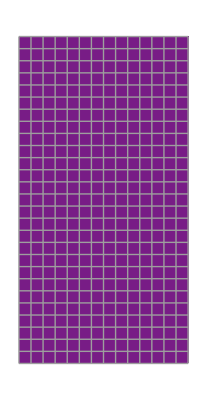

```mathematica
ArrayPlot[STCritical,Mesh-> All, ColorFunction->"Rainbow",PlotTheme->"Detailed"]
```

```mathematica
For[i=1,i<28,i++,
For[j=1,j<15,j++,

α=AlphaValues[[j]];
β=BetaValues[[i]];
A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv"];

For[n=1,n<time+1,n++,
St[[n]]=Norm[A[[n]]]
];

If[Max[St/xzero]>1.00001,STCritical[[i,j]]=0.1,
If[Max[St/xzero]<1.00001,STCritical[[i,j]]=0
]
]
]
]
```

```mathematica
ArrayPlot[STCritical,Mesh-> All, ColorFunction->"Rainbow",PlotTheme->"Detailed", PlotRange->{0,2}]
```